# WavefunctionSolver

## Tyson Jones tyson.jones@monash.edu August - September 2017

## Setup

#### Install

Permanently install the package via

```mathematica
PacletInstall["path/to/WavefunctionSolver-0.paclet"]
```

Once installed, the .paclet file may be deleted, and the package can be imported as below.

#### Import

Don’t forget the trailing ` character!

```mathematica
<< WavefunctionSolver`
```

#### Uninstall

```mathematica
PacletUninstall["WavefunctionSolver"]
```

## Plotting Wavefunctions

One can plot 1D and 2D wavefunctions specified as symbolic expressions, pure or interpolating functions or arrays or matrices.

```mathematica
?PlotWavefunction
```

PlotWavefunction[wavef, {xL, xR}] plots a 1D functional/list/numerical wavefunction between xL and xR.
PlotWavefunction[wavef, {xL, xR}, {yL, yR}] plots a 2D functional/matrix/numerical wavefunction on x ∈ [xL, xR], y ∈ [yL, yR].
PlotWavefunction[wavef, {x, xL, xR}] plots a 1D symbolic (in x) wavefunction between xL and xR.
PlotWavefunction[wavef, {x, xL, xR}, {y, yL, yR}] plots a 2D symbolic (in x and y) wavefunction on x ∈ [xL, xR], y ∈ [yL, yR].

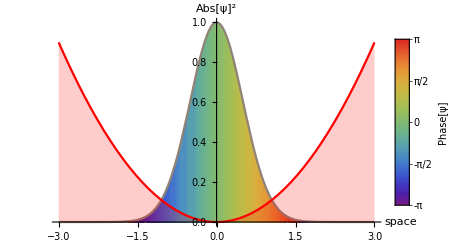

```mathematica
PlotWavefunction[
	Exp[-space^2]Exp[2 ⅈ space],
	{space, -3, 3},
	Potential -> space^2/10,
	PlotRange -> All
]
```

PlotWavefunction accepts all options for Plot, Plot3D, BarLegend and additional particular options for plotting a potential

```mathematica
Options[PlotWavefunction]
```

{Potential→None,PotentialTransform→(#1&),PotentialPlotOptions→{},ShowColorBar→True,ColorScheme→Rainbow}

Here, the potential is scaled before plotting by PotentialTransform, and the probability density and potential are separately styled.

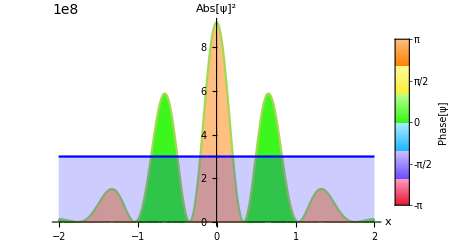

```mathematica
PlotWavefunction[
	Exp[-#1^2] HermiteH[10, #1]&,
	{-2, 2},
	Potential -> 3,
	PotentialTransform -> (10^8 # &),
	PotentialPlotOptions -> {PlotStyle -> Blue},
	ColorScheme -> "BrightBands",
	LabelStyle -> Red
]
```

The visual accuracy of plots are controlled with PlotPoints

```mathematica
PlotWavefunction[
	Sin[x] Exp[x π ⅈ]Cos[y] Exp[y π/5 ⅈ],
	{x, -π, π},
	{y, -π, π},
	Potential -> (x^2+y^2)/10,
	AxesLabel -> {"space", "space", "magnitude squared"},
	LegendLabel -> "phase",
	
	PlotPoints -> 100,
	ImageSize -> Large
]
```

-Graphics3D-

## Simulating Wavefunctions

Time-dependent wavefunctions (as symbolic expressions or functions) can be animated with PlotEvolution (which accepts all PlotWavefunction options)

```mathematica
?PlotEvolution
```

PlotEvolution[wavefunction[x, t], {x, xL, xR}, {t, t0, t1}] animates the evolution of a 1D symbolic/functional time-dependent wavefunction.
PlotEvolution[wavefunction[x, y, t], {x, xL, xR}, {y, yL, yR}, {t, t0, t1}] animates the evolution of a 2D symbolic/functional time-dependent wavefunction.
PlotEvolution[wavefunction[x], potential[x], {x, xL, xR}, duration] finds and animates the evolution of a 1D symbolic/functional/constant/array wavefunction.
PlotEvolution[wavefunction[x, y], potential[x, y], {x, xL, xR}, {y, yL, yR}, duration] finds and animates the evolution of a 2D symbolic/functional/constant/array wavefunction.

```mathematica
PlotEvolution[
	Exp[-x^2- x t] Exp[x t ⅈ],
	{x, -3, 3},
	{t, 0, 5}
]
```

```mathematica
PlotEvolution[
	Exp[-x^2-y^2] x y  Cos[x - t] Exp[ⅈ t] Exp[x ⅈ] Exp[y ⅈ / 3],
	{x, -3, 3},
	{y, -3, 3},
	{t, 0, 5},

	PlotRange -> {0, .035},
	PlotPoints :>  ControlActive[30, 100],   (* set delayed control active to render on-the-fly *)
	ImageSize -> Large
]
```

The evolution of an initial state (as a function, symbolic expression, numerical vector or matrix) under the single-particle Schrodinger equation can be found or directly plotted

```mathematica
?FindEvolution
```

FindEvolution[wavefunction[x], potential[x], {x, xL, xR}, duration] finds the evolution (returned as an interpolator f[x, t]) of a 1D symbolic/functional/constant/array wavefunction.
FindEvolution[wavefunction[x, y], potential[x, y], {x, xL, xR}, {y, yL, yR}, duration] ffinds the evolution (returned as an interpolator f[x, y, t]) of a 2D symbolic/functional/constant/array wavefunction.

```mathematica
Options[FindEvolution]
```

{EvolutionEquation→GetSchrodingerEquation,PreNormalize→True}

```mathematica
Quiet @ FindEvolution[
	{1, 2, 3, 4, 5},
	x^2,
	{x, -5, 5},
	2
]

PlotEvolution[%, {x, -5, 5}, {t, 0, 2}]
```

InterpolatingFunction[{{-5., 5.}, {0., 2.}}, <>]

```mathematica
PlotEvolution[
	Exp[-x^2/2] /.  x -> x - 1,   (* initial wavef *)
	x^2/2,                                                  (* potential *)
	{x, -6, 6},                                    (* domain *)
	4 π,                        (* duration *)
	
	PotentialTransform -> (#/30&),
	ColorScheme -> "BrightBands"
]
```

Expensive simulations can be cached by specifying the NumberOfFrames option for simultaneously high-speed and high-quality (by using a large PlotPoints option) playback, at the expense of memory

```mathematica
PlotEvolution[
	Exp[-x^2-y^2]HermiteH[1, x] HermiteH[2, y],
	(x^2+y^2)/2,
	{x, -3, 3},
	{y, -3, 3},
	3,
	NumberOfFrames -> 20,
	
	ImageSize -> Large,
	PlotRange -> {0, .7},
	PlotPoints -> 60,
	PotentialTransform -> (#/6&)
]
```

We caution that saving the above cached plot can be slow

## Finding Stationary Wavefunctions

Energy eigenfunctions and their eigenvalues of arbitrary potentials (inside an infinite potential box) can be found, or the spectrum directly plotted

```mathematica
?GetSpectrum
```

GetSpectrum[potential, domain] returns the family of {eigenvalues, eigenfunctions} of the hamiltonian associated with the given 1D potential, superposed with an infinite potential well.
GetSpectrum[potential, xDomain, yDomain] returns the family of {eigenvalues, eigenfunctions} of the hamiltonian associated with the given 2D potential, superposed with an infinite potential well.

```mathematica
?PlotSpectrum
```

PlotSpectrum[potential, domain] calculates and plots the single-particle energy-eigenfunctions of the given potential.
PlotSpectrum[domain/grid, eigvals, eigfuncs] plots the given eigensystem.
PlotSpectrum[{domain/grid, eigvals, eigfuncs}] plots the given eigensystem.

```mathematica
Options[GetSpectrum]
```

{NumberOfModes→10,NumberOfPoints→Automatic,AutoNormalize→True,OutputAsFunctions→False}

```mathematica
PlotSpectrum[
	1/2(x^2+y^2),    (* potential *)
	{x, -5, 5},
	{y, -5, 5},

	PlotRange -> {{-3,3},{-3,3},All},   (* plot domain is shrunk post-diagonalisation *)
	PlotPoints :> ControlActive[20, 80],
	PotentialTransform -> (#/10&)
]
```

```mathematica
PlotSpectrum[
	0,
	{0, 1},
	{0, 1},

	NumberOfModes -> 20,
	PlotPoints :> ControlActive[20, 80]
]
```

We can easily grab a stationary state and evolve it

InterpolatingFunction[{{-10., 10.}}, <>]

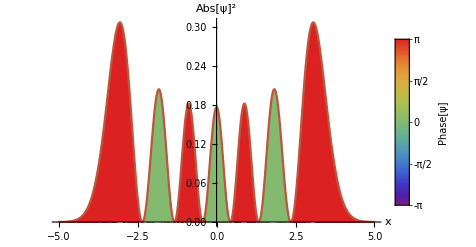

NDSolveValue::ibcinc: Warning: boundary and initial conditions are inconsistent.

```mathematica
(* GetSpectrum returns {grid, eigvals, eigfuncs} *)
GetSpectrum[
	1/2 x^2,
	{x, -10, 10},
	OutputAsFunctions -> True
][[3, 7]]

(* this is the seventh energy eigenfunction *)
PlotWavefunction[%, {x, -5, 5}, PlotRange -> All]

(* evolve it in time; only phase changes! *)
PlotEvolution[%%, 1/2 x^2,  {x, -5, 5}, 4]

(* create a coherent state by displacing the eigenmode *)
PlotEvolution[Function[{space}, %%%[space-.2]], 1/2 x^2, {x, -9, 9}, 10]
```